```mathematica
raw=Drop[Import[FileNameJoin[{NotebookDirectory[],"data/poiseuille/outsec.dat"}], "Table", "FieldSeparators"->{" "}, HeaderLines->1], -1];
```

```mathematica
cdata=Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 10]]}];
vdata=Transpose[{raw[[All, 12]], raw[[All, 13]], raw[[All, 14]]}];
pdata=raw[[All, 16]];
```

```mathematica
avgv=Mean[Sqrt[vdata[[All, 1]]^2+vdata[[All,2]]^2+vdata[[All, 3]]^2]]
```

0.00464303

```mathematica
maxv=Max[Abs[vdata]]
```

0.010218

```mathematica
l=Abs[Max[Flatten[cdata]]-Min[Flatten[cdata]]]
```

2.79658

```mathematica
nu=0.000890
```

0.00089

```mathematica
ren=avgv*l/nu
```

14.5894

```mathematica
maxren=maxv*l/nu
```

32.1072

```mathematica
arrows=Table[{Arrowheads[.01],Arrow[{
cdata[[i]],cdata[[i]]+
(vdata[[i]]/(maxv))*l*0.2
}]}, {i, Length[raw]}];
```

```mathematica
gg=Graphics3D[arrows,Axes->True,AxesLabel->{"x (m)","y (m)","z (m)"},ImageSize->Large]
```

-Graphics3D-

```mathematica
sw=0.2;
ew=1.0;
```

```mathematica
ex=0.1;
```

```mathematica
slice=Select[raw,(ex-sw<#[[8]]<ex+sw(*&&#[[9]]/l+0.5>ew/l*))&];
```

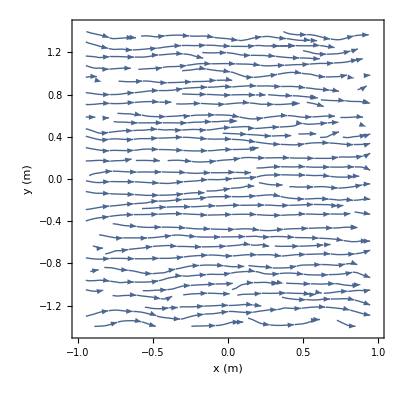

```mathematica
ListStreamPlot[Table[{{cdata[[i, 1]], cdata[[i, 2]]}, {vdata[[i, 1]], vdata[[i, 2]]}}, {i, Length[vdata]}], FrameLabel->{"x (m)","y (m)"}]
```

```mathematica
(*ListContourPlot3D[Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 10]], raw[[All, 16]]}], PlotRange->All, PlotLegends->Automatic]*)
```

```mathematica
ListDensityPlot3D[Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 10]], raw[[All, 16]]}],ColorFunction->"TemperatureMap",PlotLegends->BarLegend[All, LegendLabel->"p (Pa)"], PlotRange->All,AxesLabel->{"x (m)","y (m)","z (m)"}]
```

-Graphics3D-

```mathematica
ListDensityPlot3D[Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 10]], Sqrt[raw[[All, 12]]^2+raw[[All, 13]]^2+raw[[All, 14]]^2]}],ColorFunction->"BlueGreenYellow",PlotLegends->BarLegend[All, LegendLabel->"|u| (m/s)"], PlotRange->All]
```

-Graphics3D-

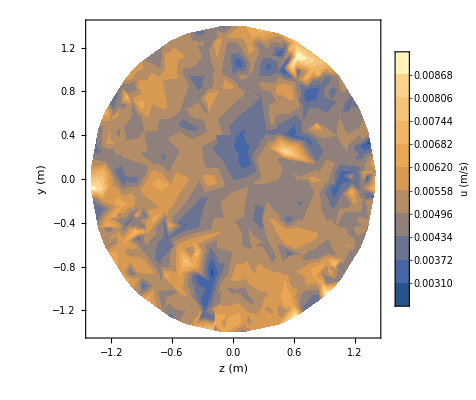

```mathematica
vmp=ListContourPlot[Transpose[{slice[[All, 10]], slice[[All, 9]], Sqrt[slice[[All, 12]]^2+slice[[All, 13]]^2+slice[[All, 14]]^2]}], PlotRange->All,ContourStyle->None, PlotLegends->BarLegend[All, LegendLabel->"u (m/s)"], Contours->10, FrameLabel->{"z (m)", "y (m)"}]
```

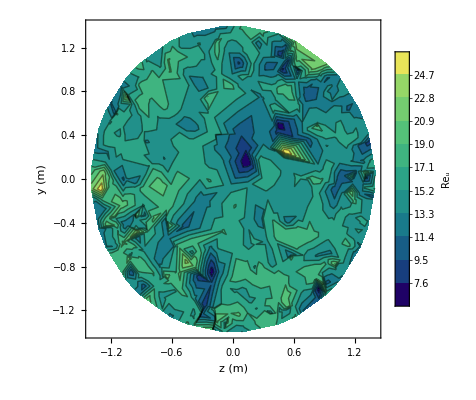

```mathematica
ListContourPlot[Transpose[{slice[[All, 10]], slice[[All, 9]], Abs[slice[[All, 12]]]*l/nu}], PlotRange->All, PlotLegends->BarLegend[All, LegendLabel->"Re_u"],ColorFunction->"BlueGreenYellow", Contours->10, FrameLabel->{"z (m)", "y (m)"}]
```

```mathematica
Graphics3D[Table[{Arrowheads[.01],Arrow[{
{slice[[i, 8]], slice[[i, 9]], slice[[i, 10]]},{slice[[i, 8]], slice[[i, 9]], slice[[i, 10]]}+
({slice[[i, 12]], slice[[i, 13]], slice[[i, 14]]}/(maxv))*l*0.2
}]}, {i, Length[slice]}],Axes->True,AxesLabel->{"x (m)","y (m)","z (m)"},ImageSize->Large]
```

-Graphics3D-

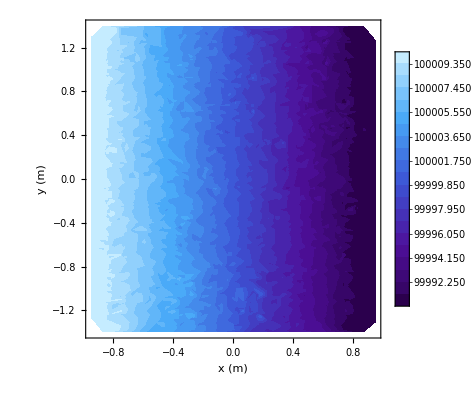

```mathematica
pxp=ListContourPlot[Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 16]]}], PlotRange->All, PlotLegends->BarLegend[All, LegendLabel->"p (Pa)"], Contours->20, ContourStyle->None, FrameLabel->{"x (m)", "y (m)"},ColorFunction->"DeepSeaColors"]
```

```mathematica
Export["~/Dropbox/pipe_pxp.pdf", pxp];
```

```mathematica
Export["~/Dropbox/pipe_vm.pdf", vmp];
```

```mathematica
ClearSystemCache[]
```

```mathematica
(Max[raw[[All, 16]]]-Min[raw[[All, 16]]])/l
```

7.17016

```mathematica
Max[raw[[All, 16]]]
```

100010.

```mathematica
Min[raw[[All, 16]]]
```

99990.

```mathematica
xv=Transpose[{Sqrt[slice[[All, 10]]^2 +slice[[All, 9]]^2 ]/Max[Sqrt[slice[[All, 10]]^2 +slice[[All, 9]]^2 ]], slice[[All, 12]]}];
```

```mathematica
fxv=Fit[xv, {1,x^2}, x]
```

0.00486391-0.0000844275 x^2

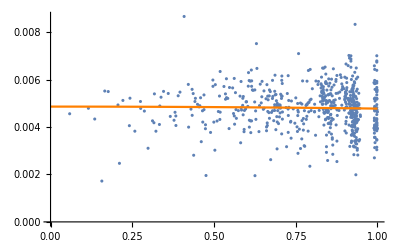

```mathematica
Show[ListPlot[xv],Plot[fxv, {x,0,1}, PlotStyle->Orange]]
```